# Binary hypothesis test plots

This notebook plots binary hypothesis tests for single and double threshold energy detectors.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

09/08/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

## Variables

Here, we define the parameters to be used:

```mathematica
M=100;
n=1;
SNRdB=0;
γ=10^(SNRdB/10);
```

```mathematica
H0:=NormalDistribution[M n,√(2M n)]
H1:=NormalDistribution[M n(1+γ),√(2M n)(1+γ)]
```

```mathematica
commonPlotOptions={Joined->True,PlotRange->Full,AxesLabel->{x,f[x]},ImageSize->400,RotateLabel->True,PlotStyle->Black};
```

## Plot

### Single threshold

```mathematica
λ=x/.FindMinimum[1-CDF[H0,x]+CDF[H1,x],{x,M n}][[2]];
```

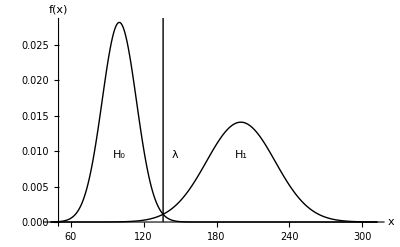

```mathematica
ListPlot[Table[{{x,PDF[H0,x]},{x,PDF[H1,x]}},{x,M n-4 √(2M n),M n(1+γ)+4 √(2M n)(1+γ)}]//Transpose,commonPlotOptions,Epilog->{{Line[{{λ,0},{λ,1}}]},Text[Subscript[H, 0],{M n,PDF[H0,M n]/3}],Text[Subscript[H, 1],{M n (1+γ),PDF[H0,M n]/3}],Text["λ",{λ+10,PDF[H0,M n]/3}]}]
```

```mathematica
Export[NotebookDirectory[]<>"binary_hypothesis_test.eps",%];
```

### Double threshold

```mathematica
pf=0.1;
pd=0.8;
```

```mathematica
λ0=x/.FindRoot[1-CDF[H0,x]==pf,{x,M n}];
λ1=x/.FindRoot[CDF[H1,x]==pd,{x,M n(1+γ)}];
```

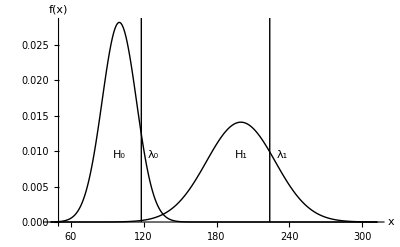

```mathematica
ListPlot[Table[{{x,PDF[H0,x]},{x,PDF[H1,x]}},{x,M n-4 √(2M n),M n(1+γ)+4 √(2M n)(1+γ)}]//Transpose,commonPlotOptions,Epilog->{Line[{{λ0,0},{λ0,1}}],Line[{{λ1,0},{λ1,1}}],Text[Subscript[H, 0],{M n,PDF[H0,M n]/3}],Text[Subscript[H, 1],{M n (1+γ),PDF[H0,M n]/3}],Text["λ_0",{λ0+10,PDF[H0,M n]/3}],Text["λ_1",{λ1+10,PDF[H0,M n]/3}]}]
```

```mathematica
Export[NotebookDirectory[]<>"binary_hypothesis_test_double_threshold.eps",%];
```